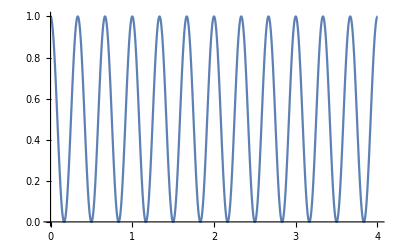

```mathematica
Plot[1/2*(1+{Sin[2*Pi*3*x+Pi/2]}),{x,0,4}]
```

```mathematica
F[x_,fr_]:=Exp[-2*Pi*I*fr*x];
G[t_] := 1/2*(1+Sin[2*Pi*3*t+Pi/2]);
Manipulate[ParametricPlot[{Re[G[t]*F[t,fr]],Im[G[t]*F[t,fr]]},{t,0,4},PlotRange->{-1,1}],{fr,0,5,0.01}]
```

```mathematica
ParametricPlot[{fr,Re[Integrate[(G[t]*F[t,fr]),{t,0,4}]]},{fr,0,5}, PlotRange->{{0,5},{-2,2}}]
```